```mathematica
b[n_] := 3 * n + 1
```

```mathematica
a[n_] := 2*n + 1
```

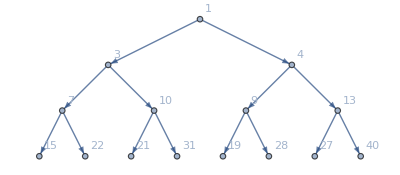

```mathematica
NestGraph[n|->{a[n], b[n]}, 1,3, VertexLabels->Automatic]
```

```mathematica
ResourceFunction["NestGraphTagged"][n↦{a[n], b[n]},{0},7,"StateLabeling"->True,PlotLegends->TraditionalForm/@{a[n],b[n]}]
```

-Graphics-

```mathematica
Graph3D[ResourceFunction["NestGraphTagged"][n↦{n+7,n+11},{0},20],VertexSize->.5,VertexStyle->Darker[RGBColor[0.9215683283650572, 0.9294118431048657, 0.9411764788496759, 1],.25]]
```

-Graphics3D-

```mathematica
With[{g=ResourceFunction["GraphRemoveLooseEnds"][ResourceFunction["NestGraphTagged"][n|->{2 n+1,3 n+1},{0},8,"StateLabeling"->True],All]},Graph[g,EdgeStyle->Catenate[EdgeList@Subgraph[g,PathGraph[First@FindPath[g,#,175],DirectedEdges->True]]/.e:DirectedEdge[_,_,t_]:>e->Directive[{RGBColor[0.91, 0.16379999999999995, 0., 1],RGBColor[0.08499999999999998, 0.39100000000000024, 0.85, 1]}[[t]],Thickness[0.02]]&/@{3,4}]
]
]
```

-Graphics-